2.5/(0.5+p)

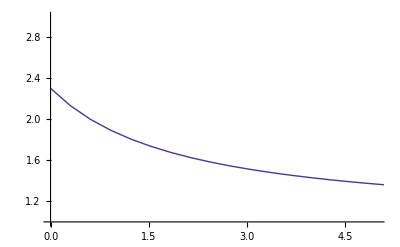

```mathematica
pstar[p_] = (2.5 / (0.5 + p))
Plot[Exp[pstar[p] / (1 + pstar[p])], {p, 0, 1000}, PlotRange->{{0, 5}, {1, 3}}]
```

```mathematica
N[Solve[{Exp[pstar[p] / (1 + pstar[p])] == 2, p≥0}, p]]
```

{{p→0.606738}}